```mathematica
dot = {{1,2},{0,1},{1,1}}
```

```mathematica
{{1,2},{0,1},{1,1}}
f = x*x
```

```mathematica
f/@{1,2,3,4}
```

{f[1],f[2],f[3],f[4]}

```mathematica
{ x -> #1, y -> #2} &@@@ dot
```

{{x→1,y→2},{x→0,y→1},{x→1,y→1}}

```mathematica
dot/.{a_,b_} -> {x-> a,y->b}
```

{{x→1,y→2},{x→0,y→1},{x→1,y→1}}

```mathematica
ClearAll[A,B,c]
```

```mathematica
A = {-1,0}
B = {1,1}
AC = 5
BC = 4
```

{-1,0}

{1,1}

5

4

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

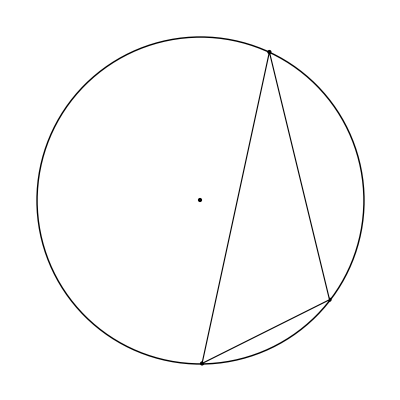

```mathematica
Show[{
Graphics@Point@A,
Graphics@Point@B,
c = 
({x,y}/. Solve[
{Norm[A - {x,y}] == 5,
Norm[B -{x,y}] == 4},
{x,y}][[2]]
);
Graphics@Point@c,
Graphics[{FaceForm[White],EdgeForm[Black], Triangle@{A,B,c}}],
o = (
{x,y}/. Solve[
{Norm[c - {x,y}] == Norm[B -{x,y}] ,
Norm[B -{x,y}] == Norm[A -{x,y}]},
{x,y}][[1]]);
Graphics@Point@o,
Graphics@Circle[o, Norm[c - o]]
}]
```